```mathematica
Clear[R, V, S, ϵ,p];
```

```mathematica
Eigenvalues[{{-R0*V-ϵ,-R0*S,-R1*S},{R0*V,R0*S-γ,0},{0,0,R1*S-1}}]
```

{-1+R1 S,1/2 (R0 S-R0 V-γ-ϵ-√((-R0 S+R0 V+γ+ϵ)^2-4 (R0 V γ-R0 S ϵ+γ ϵ))),1/2 (R0 S-R0 V-γ-ϵ+√((-R0 S+R0 V+γ+ϵ)^2-4 (R0 V γ-R0 S ϵ+γ ϵ)))}

```mathematica
Simplify[1/2 (-1-epsilon-ⅈ R+R S-R V+√((-1-epsilon-ⅈ R+R S-R V)^2+4 (-epsilon-ⅈ R+epsilon R S-R V)))]
```

1/2 (-1-epsilon-ⅈ R+R S-R V+√(4 epsilon (-1+R S)-4 R (ⅈ+V)+(1+epsilon+R (ⅈ-S+V))^2))

```mathematica
S=((R0+γ-√(R0^2-2*R0*γ+γ^2+4*p*R0*γ))/(2R0))
```

0.2 (2.5+γ-√(6.25-5. γ+10. p γ+γ^2))

```mathematica
-1+R1 S
```

-1+0.9 (2.5+γ-√(6.25-5. γ+10. p γ+γ^2))

```mathematica
p=0.35
```

0.35

```mathematica
ϵ=11/9136
```

11/9136

```mathematica
R1=4.5
```

4.5

```mathematica
R0=2.5
```

2.5

```mathematica
γ=1
```

1

```mathematica
Clear[p,γ]
```

```mathematica
f[p_]:=35./(63.-81. p)
```

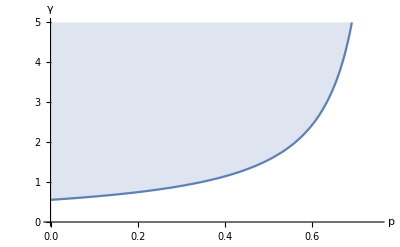

```mathematica
Plot[f[p],{p,0,1},PlotRange->{{0,0.75},{0,5}},AxesLabel->{p,γ},Filling->Top]
```

```mathematica
Solve[-1+0.9 (2.5+γ-√(6.25-5. γ+10. p γ+γ^2))==0,γ]
```

{{γ→35./(63.-81. p)}}